```mathematica
Clear["Global`*"];
```

```mathematica
cmpToPt[z_]:={Re[z],Im[z]}
checkQuad[{a_,b_,c_,d_}]:=Floor[a]==a&&a<0&&a+b+c≥d&&GCD[a,b,c,d]==1
initCord[{a_,b_,c_,d_}]:={0,-1/a-1/b,-1/a+(a-b)/(a+b)/c+I*(a+b+c-d)/(a+b)/c,-1/a+(a-b)/(a+b)/d-I*(a+b+d-c)/(a+b)/d}
expand4[{v1_,v2_,v3_,v4_}]:={{v2,v3,v4,2*(v2+v3+v4)-v1},{v1,v3,v4,2*(v1+v3+v4)-v2},{v1,v2,v4,2*(v1+v2+v4)-v3},{v1,v2,v3,2*(v1+v2+v3)-v4}}
expand3[{v1_,v2_,v3_,v4_}]:={{v2,v3,v4,2*(v2+v3+v4)-v1},{v1,v3,v4,2*(v1+v3+v4)-v2},{v1,v2,v4,2*(v1+v2+v4)-v3}}
```

```mathematica
colorDisk[r_]:=Lighter[Blue,1-0.85/r^0.75]
pairToCirc0[c_,z_]:={If[c<0,Thick,Thin],Circle[cmpToPt[z],1/Abs[c]]}
pairToCirc[c_,z_,cmax_]:=If[c<0,
{EdgeForm[Thick],FaceForm[White],Disk[cmpToPt[z],1/Abs[c]]},
{EdgeForm[Thin],FaceForm[colorDisk[c/Abs[cmax]]],Disk[cmpToPt[z],1/Abs[c]]}]
pairToText[c_,z_,cmax_]:=If[c<0,
{Text[Style[c,40,FontFamily->"Times New Roman",Bold],cmpToPt[z]+{0.8/c,0.8/c}]},
{Text[Style[c,If[c/Abs[cmax]<50,c,""],250*Abs[cmax]/c,FontFamily->"Times New Roman",Bold],cmpToPt[z]]}]
```

```mathematica
thr=50;
quad=Table[{b+c+d-2*Sqrt[b*c+c*d+d*b],b,c,d},{b,1,thr},{c,b,thr},{d,c,thr}]//Flatten//Partition[#,4]&;
cset=Select[quad,checkQuad];
```

```mathematica
cinit=cset[[12]];
zinit=initCord[cinit];
```

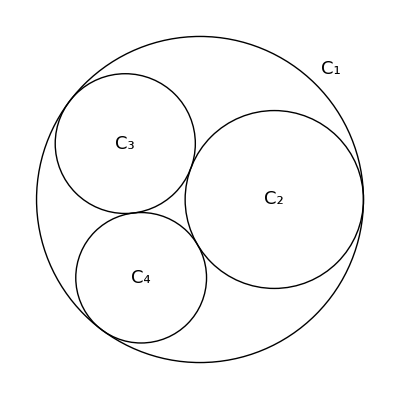

```mathematica
ginit=Graphics[{
Table[pairToCirc0[cinit[[k]],zinit[[k]]],{k,4}],
Text[Style["C_1",18,FontFamily->"Times New Roman"],0.8/Abs[cinit[[1]]]*{1,1}],
Text[Style["C_2",18,FontFamily->"Times New Roman"],cmpToPt[zinit[[2]]]],
Text[Style["C_3",18,FontFamily->"Times New Roman"],cmpToPt[zinit[[3]]]],
Text[Style["C_4",18,FontFamily->"Times New Roman"],cmpToPt[zinit[[4]]]]
}];
Show[ginit,ImageSize->400]
```

```mathematica
vc1=cinit;vcz1=cinit*zinit;
vc2=expand4[vc1];vcz2=expand4[vcz1];
vc3=expand3/@vc2//Flatten[#,1]&;vcz3=expand3/@vcz2//Flatten[#,1]&;
vc4=expand3/@vc3//Flatten[#,1]&;vcz4=expand3/@vcz3//Flatten[#,1]&;
vc5=expand3/@vc4//Flatten[#,1]&;vcz5=expand3/@vcz4//Flatten[#,1]&;
vc6=expand3/@vc5//Flatten[#,1]&;vcz6=expand3/@vcz5//Flatten[#,1]&;
vc=Join[vc2,vc3,vc4,vc5,vc6];
vcz=Join[vcz2,vcz3,vcz4,vcz5,vcz6];
vz=vcz/vc;
lenvc=Length[vc];
```

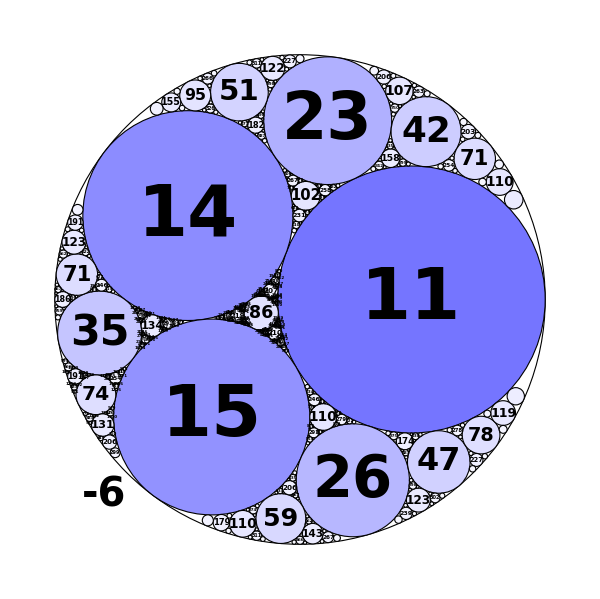

```mathematica
gpack=Graphics[{
Table[pairToCirc[cinit[[k]],zinit[[k]],cinit[[1]]],{k,4}],
Table[pairToText[cinit[[k]],zinit[[k]],cinit[[1]]],{k,4}],
Table[pairToCirc[vc[[k,4]],vz[[k,4]],cinit[[1]]],{k,lenvc}],
Table[pairToText[vc[[k,4]],vz[[k,4]],cinit[[1]]],{k,lenvc}]
}];
Show[gpack,ImageSize->600]
```